```mathematica
Subscript[CS, r] [t_]= Piecewise[{{3000, t<10000}, {3000-3(t-10000), t≥10000}}];
Subscript[CS, g][t_] = Piecewise[{{6000 - 6000/6300 t, t<6000}, {300, 6000≤t<10000}, {300 - 0.3 (t-10000), t≥1000}}];
Subscript[CS, b][t_] = Piecewise[{{100 + 2000/2100 t, t<2000}, {2000, 2000≤t<10000}, {2000-2 (t-10000), t≥1000}}];
```

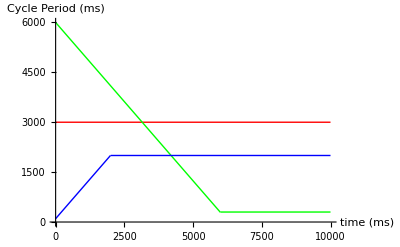

```mathematica
Plot[{Subscript[CS, r][t],Subscript[CS, g][t],Subscript[CS, b][t]},{t,0,10000}, PlotStyle->{Red,Green,Blue},PlotRange->{0,6000},AxesLabel->{"time (ms)","Cycle Period (ms)"}]
```